```mathematica
m = 1
h = 1
w = 1
hbar = h/(2Pi)
n = 1
```

1

1

1

1/(2 π)

1

```mathematica
30
```

```mathematica
30
```

```mathematica
30
```

30

```mathematica
Psin[x_,n_]:= 1/Sqrt[2^n*n!]*(m*w/(Pi*hbar))^(1/4)*Exp[-m*w*x^2/(2*hbar)]*HermiteH[n,Sqrt[m*w/hbar]*x]
```

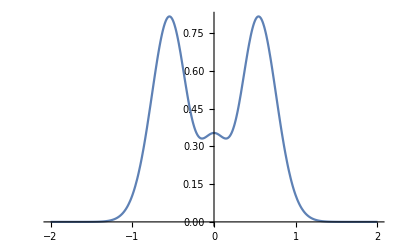

1.

```mathematica
Plot[0.5*Conjugate[Psin[x,1]]*Psin[x,1]+0.5*Conjugate[Psin[x,2]]*Psin[x,2],{x,-2,2},PlotRange->All]
Integrate[0.5*Conjugate[Psin[x,1]]*Psin[x,1]+0.5*Conjugate[Psin[x,2]]*Psin[x,2],{x,-Infinity,Infinity}]
```

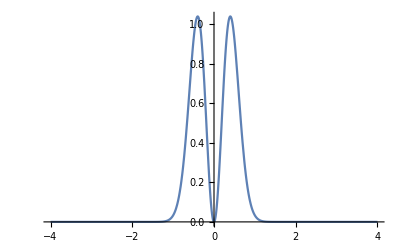
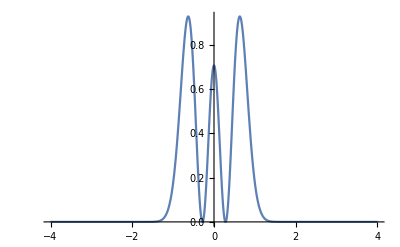
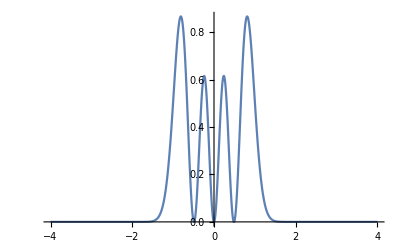
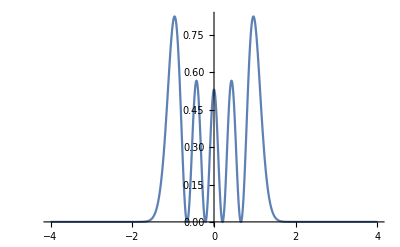
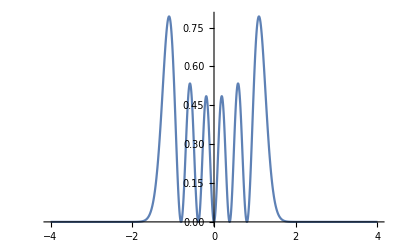
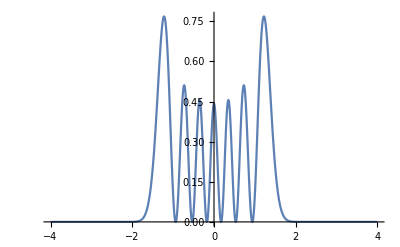
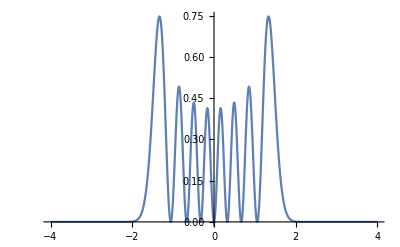
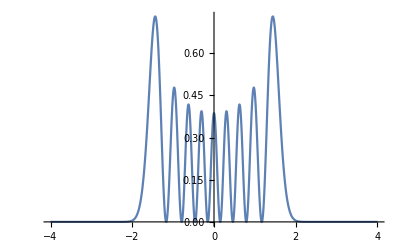

```mathematica
Table[Plot[Conjugate[Psin[x,l]]*Psin[x,l],{x,-4,4},PlotRange->All],{l,30}]
```

```mathematica
TimeEvolution[wf_,k_,t_,E_]:= wf*Exp[E*I*t/h]
```

```mathematica
Psi2D[x_,y_,nx_,ny_]:= Psin[x,nx]*Psin[y,ny]
```

```mathematica
Plot3D[Conjugate[Psi2D[x,y,30,30]]*Psi2D[x,y,30,30],{x,-4,4},{y,-4,4},PlotRange->All]
```

-Graphics3D-